401.606

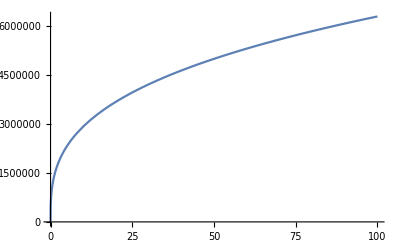

```mathematica
(* Now let's see what changes when we vary the scale at which the jump happens *)
Clear["Global`*"];



(* standard evaporation rate for SM *)
alphaSM=8.3 10^17; (* units of kg^3/s *)

tau[M0_]:=M0^3/(3 alphaSM);

(* mass as a function of time to explosion *)
SMMass[time_]:=(M0^3-3alphaSM (tau[M0]-time))^(1/3);

M0=10^7;
tau[M0]
Plot[SMMass[t],{t,0,100}]
```

```mathematica
(* Now let's see what changes when we vary the scale at which the jump happens *)
Clear["Global`*"];



(* standard evaporation rate for SM *)
alphaSM=8.3 10^17; (* units of kg^3/s *)

tau[M0_]:=M0^3/(3 alphaSM);

(* mass as a function of time to explosion *)
SMMass[time_]:=(M0^3-3alphaSM (tau[M0]-time))^(1/3);


(* Here is the photon flux; we will calculate the flux of photons integrated over some energy range *)

x[egamma_,MBH_]:=egamma/(1.058(10^10/MBH));

(* parameterization in Eq. (31-34) of 1510/.04372 *)
Aparam=6.339 10^23;
Bparam=1.1367 10^24;
ThetaS[u_]:=0.5*(1.+Tanh[10.*u]);

d2NdEdtfrag[egamma_,MBH_]:=Aparam*x[egamma,MBH ]*(1-ThetaS[x[egamma,MBH ]-0.3])+Bparam*Exp[-x[egamma,MBH ]]*ThetaS[x[egamma,MBH ]-0.3]/(x[egamma,MBH ]*(x[egamma,MBH ]+1));

Ffunc[y_]:=If[y<2,1.,Exp[-0.0962-1.982(Log[y]-1.908)*(1.+Tanh[20.*(Log[y]-1.908)])]]


d2NdEdtdirect[egamma_,MBH_]:=(1.13 10^19 (x[egamma,MBH ])^6)/(Exp[x[egamma,MBH ]]-1.)*Ffunc[x[egamma,MBH ]]

(*MBHl=10^5;
LogLogPlot[{d2NdEdtfrag[eg,MBHl],d2NdEdtdirect[eg,MBHl]},{eg,1,10^6}]*)
Elow=50. 10^-6;
Ehigh=300 10^-6.;
M0=10^7;

PhotonFlux[MBH_]:=NIntegrate[d2NdEdtfrag[egamma,MBH]+d2NdEdtdirect[egamma,MBH],{egamma,Elow,Ehigh}];

PhotonFluxTime[t_]:=PhotonFlux[SMMass[t]];

F1=0.1 PhotonFluxTime[0.001]
F2=0.9 PhotonFluxTime[0.001]

Plot[{PhotonFluxTime[t],F1},{t,0.95,1.05}]
```

3.93099×10^25

3.53789×10^26

-Graphics-

```mathematica
Elow=0.1;
Ehigh=100.;
M0=10^7;

PhotonFlux[MBH_]:=NIntegrate[d2NdEdtfrag[egamma,MBH]+d2NdEdtdirect[egamma,MBH],{egamma,Elow,Ehigh}];

PhotonFluxTime[t_]:=PhotonFlux[SMMass[t]];

F1=0.1 PhotonFluxTime[0.001]
F2=0.9 PhotonFluxTime[0.001]

Plot[{PhotonFluxTime[t],F1},{t,1.,1.2}]
```

1.52062×10^26

1.36856×10^27

-Graphics-